```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
Δ[r_]=r^2-2 M r+a^2;
Σ[r_,θ_]=r^2+a^2 Cos[θ]^2;
ρ[r_,θ_]=r+ⅈ a Cos[θ];
𝒦[r_]=(r^2+a^2) ω-a m;
```

```mathematica
ruleK={κ->Collect[Expand[𝒦[rp+rp x]]/rp/.{c_ a^2+c_ rp^2->c 2 M rp}/.{a->2 M Ω̄,ω->(ω̄)/rp},M,Factor]/.{ω̄-m Ω̄->(χ rp)/(2 M)}};
eq0=(x(x+τ))^-s D[((x(x+τ))^(s+1)R'[x]), x]+((κ^2-I s(2x+τ)κ)/(x(x+τ))-λ+4I s ω̄ (1+x))R[x];
Eq=eq0/.ruleK;
```

```mathematica
h[l_]=((l^2-(kp+km)^2) (l^2-(kp-km)^2) (l^2-s^2))/(2 (l^2-1/4) l^3)/.{kp+km->Max[Abs[s],Abs[l]],kp-km->(s m)/Max[Abs[s],Abs[l]]};
EigenCoef={l(1+l)-s(s+1),-(2 m s^2)/(l (1+l)),h[l+1]-h[l]-1,(2 h[l] m s^2)/((l-1) l^2 (l+1))-(2 h[l+1] m s^2)/((l+1)^2 l (l+2)),m^2 s^4 ((4 h[l+1])/(l^2 (l+1)^4 (l+2)^2)-(4 h[l])/((l-1)^2 l^4 (l+1)^2))-((l+2) h[l+1] h[l+2])/(2 (l+1) (2 l+3))+h[l+1]^2/(2 (l+1))+(h[l] h[l+1])/(2 l (l+1))-h[l]^2/(2 l)+((l-1) h[l-1] h[l])/(2 l (2 l-1)),m^3 s^6 ((8 h[l])/(l^6 (l+1)^3 (l-1)^3)-(8 h[l+1])/(l^3 (l+1)^6 (l+2)^3))+m s^2 h[l] (-(h[l+1] (7 l^2+7 l+4))/(l^3 (l+2) (l+1)^3 (l-1))-(h[l-1] (3 l-4))/(l^3 (l+1) (2 l-1) (l-2)))+m s^2 (((3 l+7) h[l+1] h[l+2])/(l (l+1)^3 (l+3) (2 l+3))-(3 h[l+1]^2)/(l (l+1)^3 (l+2))+(3 h[l]^2)/((l-1) l^3 (l+1)))};
```

```mathematica
RuleR={R->Function[x,(x/τ)^(-s-ⅈ χ/τ)f[x]]};
nCoef=10;
RuleF={f->Function[x,∑_(n=0)^nCoef 𝒶[n] x^n]};
EquationF=PowerExpand@Simplify[(x/τ)^(s+ⅈ χ/τ)x (x+τ) (Eq/.RuleR)];
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[(λ+s(s+1))^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+EigenCoef.Table[((𝒥 ω̄)/rp)^n,{n,0,Length[EigenCoef]-1}]/.l->l+ϵ};
```

```mathematica
RuleBoundaryBHole={𝒶[0]->1};
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_]:=Limit[PowerExpand[#1//.RuleParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}],ϵ->0]&;
```

```mathematica
x0=10^-14.;
xM:=4000/ω̄;
Omega=DeleteCases[Range[0.001,0.55,0.004],ReplaceParams[1,1,1,0.9][m Ω̄]];
Spin={0.2,0.4,0.6,0.8,0.9,0.99,0.999};
```

```mathematica
ClearAll@SolveωF;
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ]:=SolveωF[𝓈,ℓ,𝓂,#,Range[0.001,0.55,0.004]]&/@Flatten[{𝒿}]
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ,{omega__?NumberQ}]/;And@@Thread[0<𝒿<1]&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
({Print["𝓈 = ",𝓈,"; 𝒥 = ",#1];#1,
Block[{CoefList,SolCoef,SolF,eqF,ωlist},
ωlist=DeleteCases[{omega},ReplaceParams[𝓈,𝓂,ℓ,#1][m Ω̄]];eqF=ReplaceParams[𝓈,𝓂,ℓ,#1][EquationF];CoefList=Rationalize[CoefficientList[eqF/.RuleF,x]⟦1;;nCoef+1⟧];SolCoef=Rationalize[Chop[First[Solve[CoefList==0,Evaluate[Table[𝒶[n],{n,1,nCoef}]]]]]];SolF=ParallelTable[First@NDSolve[{eqF==0,{f[x0],f'[x0]}==({f[x0],f'[x0]}/.RuleF/.SolCoef/.RuleBoundaryBHole)},f,{x,x0,xM}],{ω̄,ωlist}];Transpose[{Thread[ω̄->ωlist],First/@SolF}]]
}&)/@Flatten[{𝒿}];
```

```mathematica
SolωF0=SolveωF[1,1,1,Spin,Omega];
SolωF2=SolveωF[-1,1,1,Spin,Omega];
```

𝓈 = 1; 𝒥 = 0.2

𝓈 = 1; 𝒥 = 0.4

𝓈 = 1; 𝒥 = 0.6

𝓈 = 1; 𝒥 = 0.8

𝓈 = 1; 𝒥 = 0.9

𝓈 = 1; 𝒥 = 0.99

𝓈 = 1; 𝒥 = 0.999

𝓈 = -1; 𝒥 = 0.2

𝓈 = -1; 𝒥 = 0.4

𝓈 = -1; 𝒥 = 0.6

𝓈 = -1; 𝒥 = 0.8

𝓈 = -1; 𝒥 = 0.9

𝓈 = -1; 𝒥 = 0.99

𝓈 = -1; 𝒥 = 0.999

```mathematica
Z0=({ω̄,ReplaceParams[1,1,1,First[#]][-(ω̄/χ)/Abs[f[xM]]^2]}/.Last[#]&)/@SolωF0;
Z2=({ω̄,ReplaceParams[-1,1,1,First[#]][-1/(1+(ℬ^2 τ^8 Abs[f[xM]]^2)/(ω̄ χ(τ^2+χ^2)))]}/.Last[#]&)/@SolωF2;
```

```mathematica
EmptyCircle=Graphics[{EdgeForm[AbsoluteThickness[1.4]],White,Disk[{0,0},1]}];
testZ=ListLogPlot[{Abs@Z0⟦#1⟧,Abs@Z2⟦#1⟧},PlotRange->All,Frame->True,ImageSize->500,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},Joined->True,PlotLabel->"𝒥 = "<>ToString[Spin[[#1]]],
PlotLegends->Placed[{"s=1","s=-1"},{Center,Bottom}]
]&/@Range@Length@Spin//Partition[#,UpTo@2]&//GraphicsGrid[#,ImageSize->1100,Spacings->{0,-100}]&;
Export["Data/testZ.pdf",testZ];
```

```mathematica
(*Export["Data/Z_1_1_1_0.9.csv",Z];
EmptyCircle=Graphics[{EdgeForm[AbsoluteThickness[1.4]],White,Disk[{0,0},1]}];
Plot1=ListPlot[Z,PlotRange->All,Joined->True,MeshStyle->EdgeForm[Blue],PlotStyle->Blue,Frame->True,ImageSize->600,PlotMarkers->{EmptyCircle,0.025},BaseStyle->{FontFamily->"Helvetica",FontSize->14}];
Plot1*)
```

```mathematica
Normal@Series[(x/τ)^(-s-(ⅈ χ)/τ) 𝒜 (x/τ+1)^((ⅈ χ)/τ) Hypergeometric2F1[-l,1+l,1-s-(2ⅈ χ)/τ,-x/τ],{x,0,3}]//PowerExpand//Simplify
```

x^(-s-(ⅈ χ)/τ) 𝒜 τ^(s+(ⅈ χ)/τ) (1+x ((l (1+l))/(τ-s τ-2 ⅈ χ)+(ⅈ χ)/τ^2)+1/2 x^2 (((-1+l) l (1+l) (2+l))/(((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))-(2 ⅈ l (1+l) χ)/(τ^2 ((-1+s) τ+2 ⅈ χ))-(χ (ⅈ τ+χ))/τ^4)+1/6 x^3 (-((-2+l) (-1+l) l (1+l) (2+l) (3+l))/(((-3+s) τ+2 ⅈ χ) ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))+(3 ⅈ (-1+l) l (1+l) (2+l) χ)/(τ^2 ((-2+s) τ+2 ⅈ χ) ((-1+s) τ+2 ⅈ χ))+(3 l (1+l) χ (ⅈ τ+χ))/(τ^4 ((-1+s) τ+2 ⅈ χ))+(χ (2 ⅈ τ^2+3 τ χ-ⅈ χ^2))/τ^6))

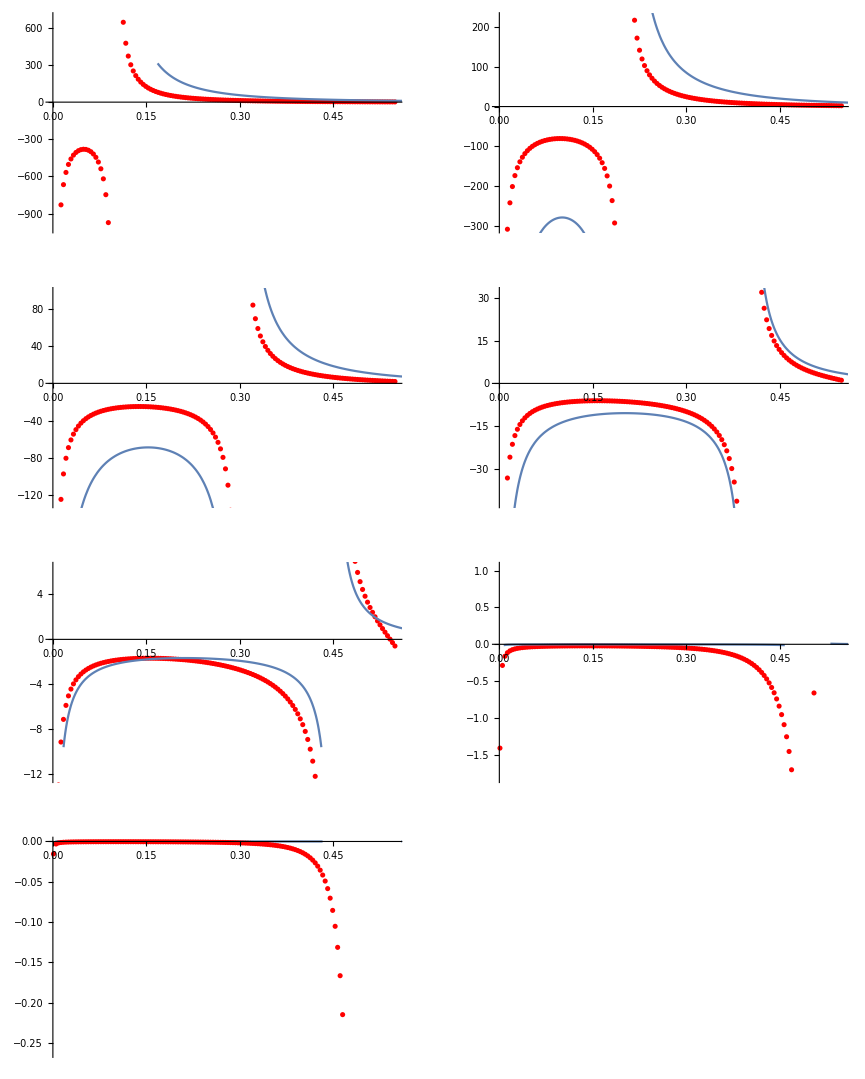

```mathematica
Show@@@({ListPlot[{Z0[[#,All,1]],(-(Z0[[#,All,2]])^-1-1)/(Abs[f[xM]]^2/.SolωF2[[#,2]])}ᵀ,PlotStyle->Red,ImageSize->400],Plot[(ℬ^2 τ^8)/(ω̄ χ(τ^2+χ^2))//ReplaceParams[1,1,1,SolωF2[[#,1]]]//Evaluate,{ω̄,0,0.7}]}&/@Range@Length@Spin)//Partition[#,UpTo@2]&//GraphicsGrid
```